```mathematica
D1=DL(1-(DL+D0)/(DL-D0)(1+d/DL)+(2D0)/(DL-D0)*l2/f+(DL+D0)/(DL-D0)*(1+d/DL)*h/(l2+h));
l1=(DL-D0)/DL/(1/f-(1+d/DL)*1/(l2+h));
```

```mathematica
DL=24;
D0=22;
h=75;
```

```mathematica
Foo[ff_,dd_]:=Module[{l2m=(dd/DL+1)ff-h, l2M, rt, opt, l1opt, l2opt},rt = FindRoot[32==D1/.{f->ff,d->dd},{l2,10}];l2M = l2/.rt;Print["l2 min = ",l2m, ", l2 max = ",l2M, "\n"];
opt=NMinimize[{l2+l1/.{f->ff,d->dd},l2M>l2>Max[l2m,0]},l2];l2opt = l2/.opt[[2]];l1opt=(l1/.{f->ff,d->dd,l2->l2opt});
Print["l1+l2 minimum: ",opt,"\t v1=",1/(1/ff-1/l1opt),"\tD0'=",D0*-ff/(l1opt-ff) ];Plot[l1/.{f->ff,d->dd},{l2,Max[l2m,0],l2M},PlotLabel->"l1"]
(*Plot[32-D1/.{f->ff,d->dd},{l2,Max[l2m,0],l2/.rt},PlotLabel->"32-D1"]*)]
```

l2 min = 25/2, l2 max = 21.5656

l1+l2 minimum: {88.1396,{l2→21.5656}}	 v1=-592.575	D0'=195.822

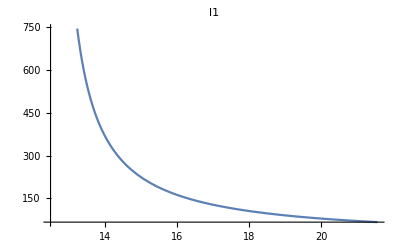

```mathematica
Foo[75,4]
```

l2 min = 75/8, l2 max = 18.8645

l1+l2 minimum: {80.686,{l2→18.8645}}	 v1=-351.831	D0'=125.204

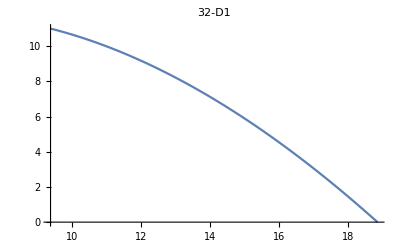

```mathematica
Foo[75,3]
```

l2 min = -25/2, l2 max = 5.90655

l1+l2 minimum: {33.3786,{l2→5.90655}}	 v1=-43.3514	D0'=34.7164

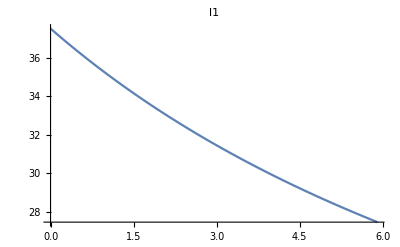

```mathematica
Foo[75,-4]
```

l2 min = -50/3l2 max = 3.40909

{18.75,{l2→0.}}

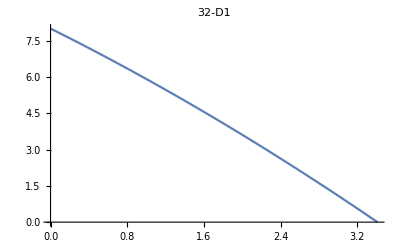

```mathematica
Foo[50,4]
```

l2 min = -175/12l2 max = 3.81476

{21.3157,{l2→1.28286}}

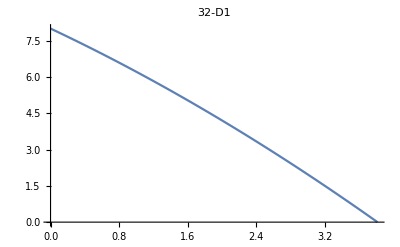

```mathematica
Foo[50,5]
```

l2 min = -25/3

l2 max = 5.60023

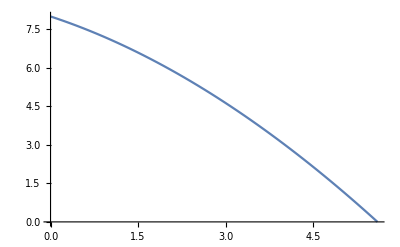

```mathematica
Foo[50,8]
```

```mathematica
Foo[ff_,dd_]:=Module[{l2m=(dd/DL+1)ff-h, l2M, rt, opt, v1},rt = FindRoot[32==D1/.{f->ff,d->dd},{l2,10}];l2M = l2/.rt;Print["l2 min = ",l2m, ", l2 max = ",l2M, "\n"];
v1=1/(1/ff-1/l1/.{f->ff,d->dd});
Plot[Min[D0*Abs[v1/(l1/.{f->ff,d->dd})/(l2+h-v1)], DL/(l2+h)],{l2,Max[l2m,0],l2M},PlotLabel->"Span Angle from Center"]]
```

l2 min = 25/2, l2 max = 21.5656

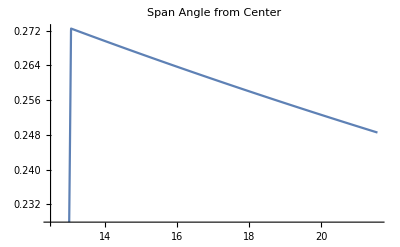

```mathematica
Foo[75,4]
```

```mathematica
D1=DL(1-(DL+D0)/(DL-D0)(1-d/DL)+(2D0)/(DL-D0)*l2/f+(DL+D0)/(DL-D0)*(1-d/DL)*h/(l2+h));
l1=(DL-D0)/DL/(1/f-(1-d/DL)*1/(l2+h));
```

```mathematica
Goo[ff_,dd_]:=Module[{l2m=(-dd/DL+1)ff-h, l2M, rt, opt, v1},rt = FindRoot[32==D1/.{f->ff,d->dd},{l2,10}];l2M = l2/.rt;Print["l2 min = ",l2m, ", l2 max = ",l2M, "\n"];
(*opt=NMaximize[{l2+l1/.{f->ff,d->dd},l2M>l2>Max[l2m,0]},l2];*)v1=1/(1/ff-1/l1/.{f->ff,d->dd});
Plot[Min[D0*Abs[v1/(l1/.{f->ff,d->dd})/(l2+h-v1)], DL/(l2+h)],{l2,Max[l2m,0],l2M},PlotLabel->"Span Angle from Center"](*
Print["l1+l2 minimum: ",opt,"\t v1=",,"\tD0'=",D0*-ff/(l1opt-ff) ]*)(*;Plot[l1/.{f->ff,d->dd},{l2,Max[l2m,0],l2M},PlotLabel->"l1"]*)]
```

l2 min = -25/2, l2 max = 5.90655

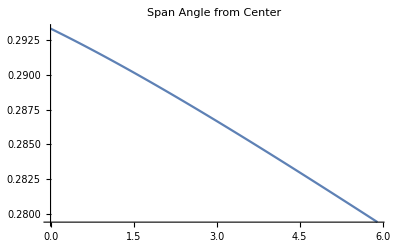

```mathematica
Goo[75,4]
```

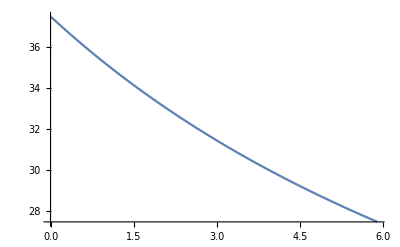

```mathematica
Plot[l1/.{f->75,d->4},{l2,0,5.9}]
```

```mathematica
N[l1/.{f->75,d->4,l2->5}]
```

28.5714

l2 min = -100/3, l2 max = 1.75183

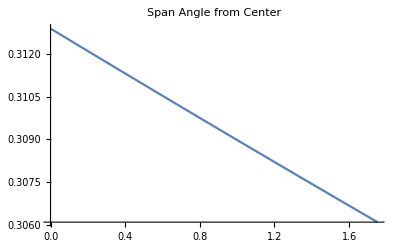

```mathematica
Goo[50,4]
```

```mathematica
PostProcessing
```

```mathematica
DL=24;
D0=22;
Dw=34;
h=78;
```

```mathematica
D1=DL(1-(DL+D0)/(DL-D0)(1-d/DL)+(2D0)/(DL-D0)*l2/f+(DL+D0)/(DL-D0)*(1-d/DL)*h/(l2+h));
l1=(DL-D0)/DL/(1/f-(1-d/DL)*1/(l2+h));
```

```mathematica
NSolve[(l1/.{d->2})==40,l2]
```

{{l2→3.48148}}

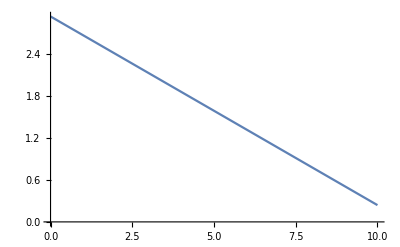

```mathematica
Plot[d/.First[NSolve[(l1/.{l2->l2a})==40,d]],{l2a,0,10}]
```

```mathematica
D1 = DL(1+(l2(D0+DL))/(l1 DL)-l2/f);
```

```mathematica
Df=20;
lf=35;
```

```mathematica
Clear[l1]
```

```mathematica
l3=(1/f-1/Min[((lf DL)/(DL-Df)),(l1 DL)/(DL-D0)])^-1;
```

```mathematica
d = -DL((l2+h)/l3-1);
```

```mathematica
Table[d100/.{l1->l1a},{l1a,{40,50,60}}]
```

{-24 (-1+(19 (78+l2))/2400),-24 (-1+(78+l2)/120),-24 (-1+(31 (78+l2))/3600)}

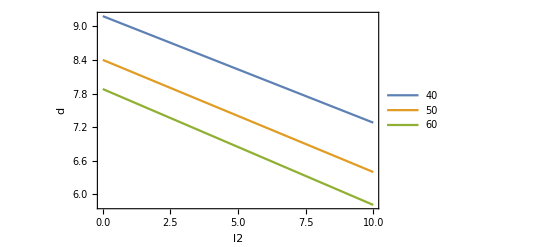

```mathematica
Plot[Evaluate[Table[d/.{f->100,l1->l1a},{l1a,{40,50,60}}]],{l2,0,10},PlotLegends->{40,50,60},Frame->True,FrameLabel->{"l2","d"}]
```

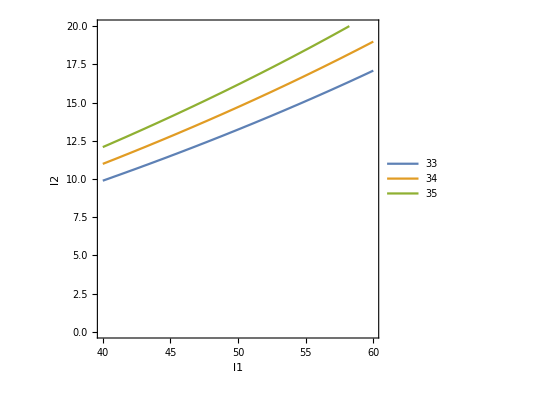

```mathematica
ContourPlot[Evaluate[Table[(D1/.{f->100})==Dww,{Dww,Dw-1,Dw+1,1}]],{l1,40,60},{l2,0,20},PlotLegends->Table[Dww,{Dww,Dw-1,Dw+1,1}], FrameLabel->{"l1","l2"}]
```

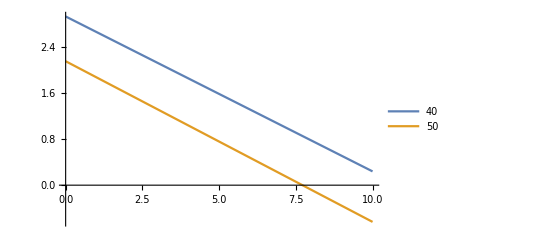

```mathematica
d75=d/.{f->75};
Plot[{d75/.{l1->40},d75/.{l1->50}},{l2,0,10},PlotLegends->{40,50}]
```

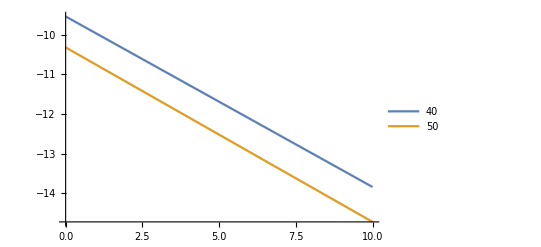

```mathematica
d50=d/.{f->50};
Plot[{d50/.{l1->40},d50/.{l1->50}},{l2,0,10},PlotLegends->{40,50}]
```

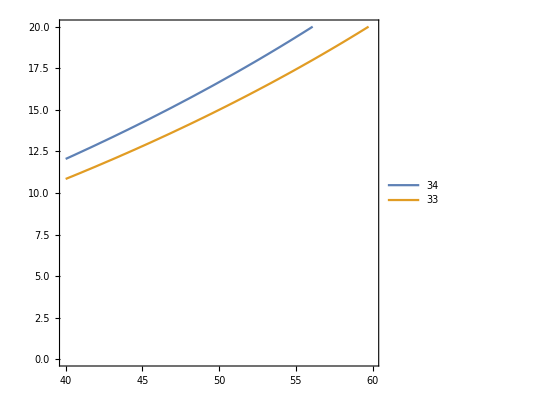

```mathematica
ContourPlot[{(D1/.{f->75})==Dw,(D1/.{f->75})==Dw-1},{l1,40,60},{l2,0,20},PlotLegends->{Dw,Dw-1}]
```

```mathematica
{D1,(D1-DL)/l2,d,l3,l2+h}/.{l1->40,f->75.0,l2->3.0}
```

{26.49,0.83,7.33714,116.667,81.}

```mathematica
{D1,(D1-DL)/l2,d,l3,l2+h}/.{l1->40,f->100.0,l2->3.0}
```

{26.73,0.91,13.8171,190.909,81.}